Piecewise[{{0, t<0}, {1, t≥0}, {0, True}}]

Piecewise[{{0, t<0}, {t, t≥0}, {0, True}}]

Piecewise[{{1, Abs[t]<0.5}, {0, True}}]

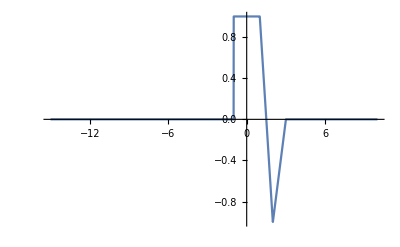

```mathematica
U[t_]=Piecewise[{{0,t<0},{1,t>=0}}]
  R[t_]=Piecewise[{{0,t<0},{t,t>=0}}]
  S[t_]=Piecewise[{{1,Abs[t]<0.5},{0,Abs[t]>0.5}}]
  Plot[U[t+1]-2*R[t-1]+3*R[t-2]-R[t-3],{t,-15,10},Exclusions->None]
```

```mathematica
Piecewise[{{0, t<0}, {1, t≥0}, {0, True}}]
```

Piecewise[{{0, t<0}, {1, t≥0}, {0, True}}]

Cos[(2 π t)/3]+Sin[4 π t]

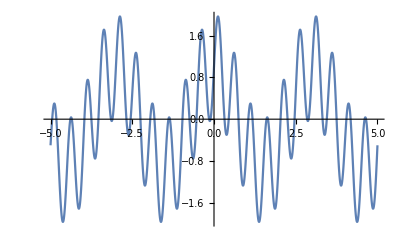

Cos[(π t)/8] Sin[(π t)/4]

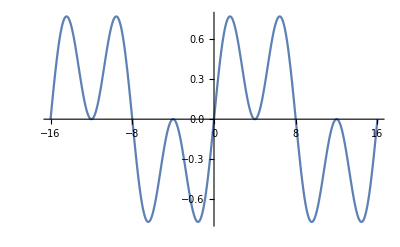

t Sin[1/t]

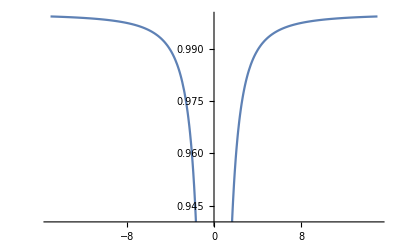

(Piecewise[{{0, -1+t^2<0}, {1, -1+t^2≥0}, {0, True}}]) Sinc[12 t]

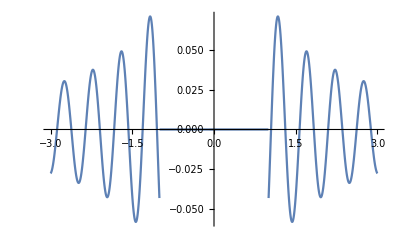

(Piecewise[{{0, -1+t<0}, {-1+t, -1+t≥0}, {0, True}}]) (Piecewise[{{0, Sin[π t]<0}, {1, Sin[π t]≥0}, {0, True}}])

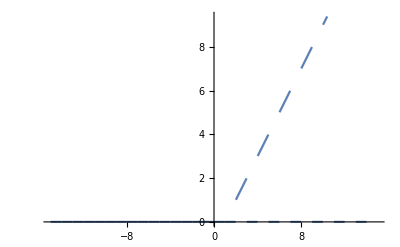

Piecewise[{{-2, t<-2}, {Piecewise[{{0, t<0}, {t, t≥0}, {0, True}}], -2<t<2}, {ⅇ^(-2 t), t>2}, {0, True}}]

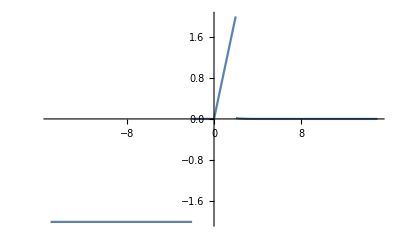

```mathematica
X2[t_]=Sin[4*Pi*t]+Cos[(2*Pi*t)/3]
Plot[X2[t],{t,-5,5}]
X3[t_]=Sin[(Pi*t)/4]*Cos[(Pi*t)/8]
Plot[X3[t],{t,-16,16}]
X4[t_]=Sin[1/t]*t
Plot[X4[t],{t,-15,15}]
X5[t_]=Sinc[12*t]*U[t^2-1]
Plot[X5[t],{t,-3,3}]
X6[t_]=U[Sin[Pi*t]]*R[t-1]
Plot[X6[t],{t,-15,15}]
X7[t_]=Piecewise[{{-2,t<-2},{R[t],-2<t <2},{Exp[-2*t],t>2}}]
Plot[X7[t],{t,-15,15}]
```

```mathematica
FunctionPeriod[X2[t],t]
FunctionPeriod[X3[t],t]
FunctionPeriod[X4[t],t]
FunctionPeriod[X5[t],t]
FunctionPeriod[X6[t],t]
FunctionPeriod[X7[t],t]
```

3

16

0

0

0

«1 more identical outputs»

```mathematica
energy[x_]:=Integrate[x[t]^2,{t,-Infinity,Infinity}]
P[X_]:=Limit  [(1/(2*T))*Integrate[X[t]^2,{t,-T,T}],T-> Infinity]
DC[X_]:=Limit  [(1/(2*T))*Integrate[X[t],{t,-T,T}],T-> Infinity]
px[1]=P[X5]
DCx[1]=DC[X5]
ex[1]=energy[X5] //N
```

Integrate::pwrl: Unable to prove that integration limits {-T,T} are real. Adding assumptions may help.

0

Integrate::pwrl: Unable to prove that integration limits {-T,T} are real. Adding assumptions may help.

Integrate::idiv: Integral of (Cos[(2 π t)/3]+Sin[4 π t])^2 does not converge on {-∞,∞}.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.81037×10^7}. NIntegrate obtained 576234. and 483236. for the integral and error estimates.

```mathematica
X8[t_]=2*Sin[Pi*t/3]

Plot[X8[t],{t,-3,3}]
sample[t_]=Sum[X8[0.1*n]*S[t-0.1n],{n,-30,30}];
Plot[sample[t],{t,-3,3}]
```

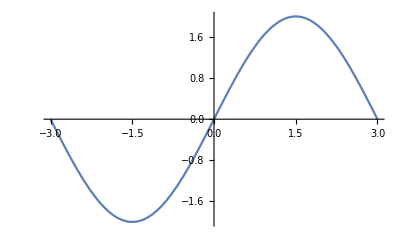

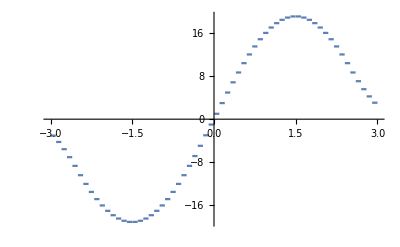

```mathematica
2 Sin[(π t)/3]
```